```mathematica
Energy[kx_,ky_]:=t*Sqrt[1+4*Cos[kx*a/2]Cos[Sqrt[3]ky*a/2]+4Cos[kx*a/2]^2]/.t->1/.a->1
```

```mathematica
MyRegion=DiscretizeRegion[Polygon[2/Sqrt[3]*{{2Pi/Sqrt[3],0},{Pi/Sqrt[3],Pi},{-Pi/Sqrt[3],Pi},{-2Pi/Sqrt[3],0},{-Pi/Sqrt[3],-Pi},{Pi/Sqrt[3],-Pi}}],MaxCellMeasure->{"Area"->0.00001}]
```

```mathematica
Epoints=Apply[Energy,MeshCoordinates[MyRegion],{1}]
```

```mathematica
Export["Epoints.mat",Epoints]
```

```mathematica
{Emin,Emax}=MinMax[Epoints]
```

```mathematica
dE=.01;
```

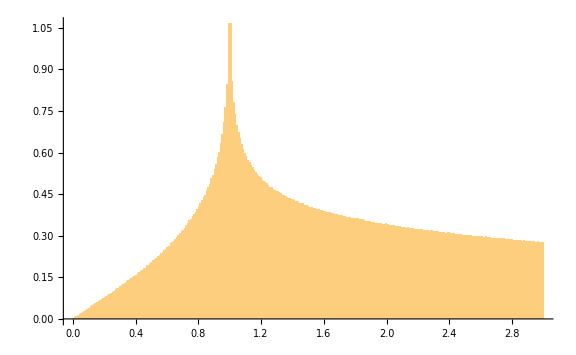

```mathematica
Histogram[Epoints,{Emin,Emax,dE},"ProbabilityDensity",ImageSize->Large]
```